```mathematica
Clear["Global`*"]

eqn={-3/2+(-1/2+a-b)x+(a+b)(x^2-y^2)==0,(1/2+a-b)y-2(a+b)x*y==0}
```

{-3/2+(-1/2+a-b) x+(a+b) (x^2-y^2)==0,(1/2+a-b) y-2 (a+b) x y==0}

```mathematica
Solve[eqn,{x,y}]
```

{{x→(1+2 a-2 b)/(4 (a+b)),y→-(√(-1-20 a+12 a^2-28 b-24 a b+12 b^2))/(4 √(a^2+2 a b+b^2))},{x→(1+2 a-2 b)/(4 (a+b)),y→(√(-1-20 a+12 a^2-28 b-24 a b+12 b^2))/(4 √(a^2+2 a b+b^2))},{x→(1-2 a+2 b-√(1+20 a+4 a^2+28 b-8 a b+4 b^2))/(4 (a+b)),y→0},{x→(1-2 a+2 b+√(1+20 a+4 a^2+28 b-8 a b+4 b^2))/(4 (a+b)),y→0}}

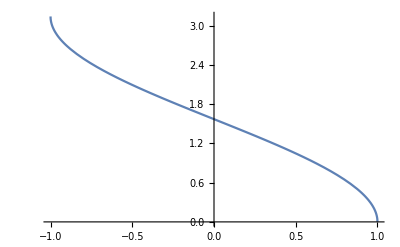
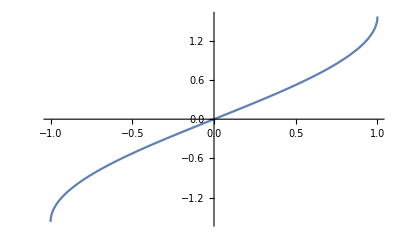

```mathematica
List[Plot[ArcCos[x],{x,-1,1}],Plot[ArcSin[x],{x,-1,1}]]
```

t+2 δ+4 t δ==0

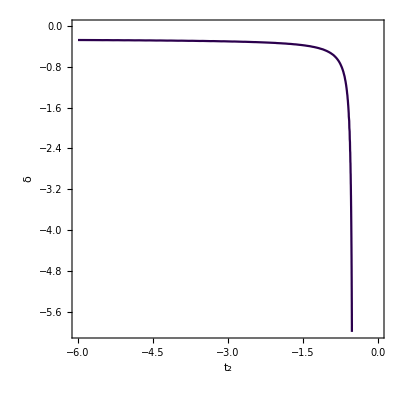

```mathematica
Clear["Global`*"]
eqa=t+2δ+4δ t==0
ContourPlot[t+2δ+4δ t==0,{t,-6,0},{δ,-6,0},FrameLabel->{Style[Subscript[t, 2],Large,Bold],Style[δ,Large,Bold]},ColorFunction->"DeepSeaColors"]
```

```mathematica
Clear["Global`*"]
dx:=u+(v+t-δ)*x+(t+δ)*(x^2-y^2)
dy:=(-v+t-δ)*y-2(t+δ)*x*y
eqn={dx==0,dy==0,x^2+y^2==1}
Reduce[eqn,{x,y}]
Solve[Drop[eqn,-1],{x,y}]
```

{u+x (t+v-δ)+(x^2-y^2) (t+δ)==0,y (t-v-δ)-2 x y (t+δ)==0,x^2+y^2==1}

(u==v-2 δ&&t==-v+δ&&(x==-1||x==1)&&y==0)||(u==v-2 δ&&t+v-δ≠0&&x==-1&&y==0)||(δ==0&&u==v&&t≠0&&x==(t-v)/(2 t)&&(y==-√(1-x^2)||y==√(1-x^2)))||(δ==0&&v==0&&u==0&&t==0&&(y==-√(1-x^2)||y==√(1-x^2)))||(u-v-4 δ≠0&&t==(-u δ-v δ)/(u-v-4 δ)&&t≠0&&x==(2 t-u-v)/(4 t)&&(y==-√(1-x^2)||y==√(1-x^2)))||(u-v+2 δ≠0&&t==1/2 (-u-v)&&t+v-δ≠0&&x==(-t-u-δ)/(t+v-δ)&&y==0)||(u==-v&&t==0&&δ≠0&&x==(-v-δ)/(2 δ)&&(y==-√(1-x^2)||y==√(1-x^2))&&v+2 δ≠0)||(v==-2 δ&&u==2 δ&&t==0&&x==1/2&&(y==-(√3)/2||y==(√3)/2)&&δ≠0)||(δ≠0&&v==-2 δ&&u==v+4 δ&&t≠0&&x==(t-v-2 δ)/(2 t)&&(y==-√(1-x^2)||y==√(1-x^2)))

{{x→(t-v-δ)/(2 (t+δ)),y→-(√(3 t^2+4 t u-2 t v-v^2-6 t δ+4 u δ+2 v δ+3 δ^2))/(2 √(t^2+2 t δ+δ^2))},{x→(t-v-δ)/(2 (t+δ)),y→(√(3 t^2+4 t u-2 t v-v^2-6 t δ+4 u δ+2 v δ+3 δ^2))/(2 √(t^2+2 t δ+δ^2))},{x→(-t-v+δ-√((t+v-δ)^2-4 u (t+δ)))/(2 (t+δ)),y→0},{x→(-t-v+δ+√((t+v-δ)^2-4 u (t+δ)))/(2 (t+δ)),y→0}}

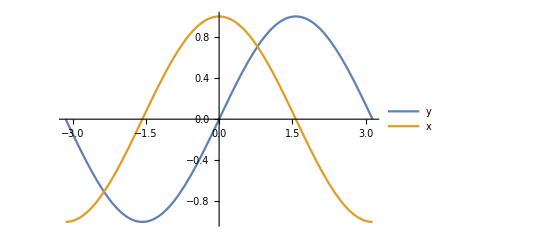

```mathematica
Module[{x},
Plot[{Sin[x],Cos[x]},{x,-π,π},PlotLegends->{"y","x"}]
]
```

```mathematica
(t-δ-v)^2//Expand
```

t^2-2 t v+v^2-2 t δ+2 v δ+δ^2

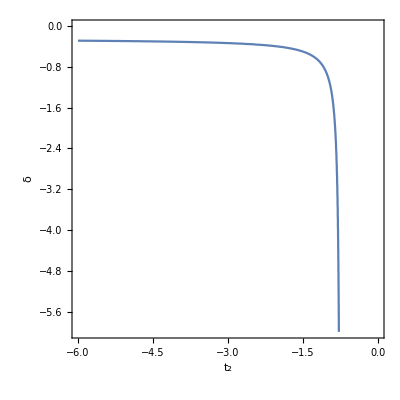

```mathematica
Module[{t1=-3/2,τ=-1/2},
u=t1+τ;v=t1-τ;
g=ContourPlot[-t2 v+v δ+t2 u+u δ-4t2 δ==0,{t2,-6,0},{δ,-6,0},FrameLabel->{Style[Subscript[t, 2],Large,Bold],Style[δ,Large,Bold]}]
]
```

```mathematica
Module[{t1=-3/2,τ=-1/2,δ=-4},
u=t1+τ;v=t1-τ;
Solve[-t2 v+v δ+t2 u+u δ-4t2 δ==0,t2]
]
```

{{t2→-4/5}}

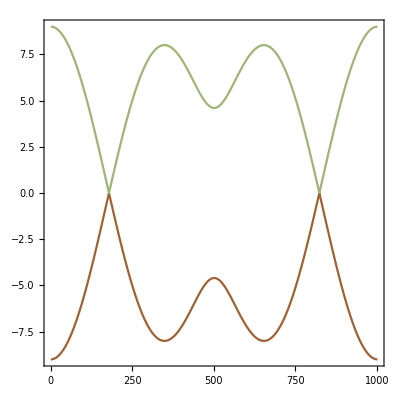

```mathematica
hamiltonian[kx_]:=Module[{tg,tk,ty,tp,h},
tk=t1+τ;
tg=t1-τ;
ty=t2+δ;
tp=t2-δ;
h=Table[0,2,2];
h[[1,2]]=tk+tg*Exp[-ⅈ kx]+tp*Exp[ⅈ kx]+ty*Exp[-2ⅈ kx];
h[[2,1]]=Conjugate@h[[1,2]];
Return[h]
]
el=ParallelTable[Sort@Eigenvalues[hamiltonian[kx]/.{t1->-3/2,τ->-1/2,t2->-4/5,δ->-4}],{kx,-π,π,0.001*2π}];
ListPlot[Transpose[Re[el]],Frame->True,AspectRatio->1,Joined->True,ColorFunction->"SouthwestColors"]
```